```mathematica
Clear["Global`*"]
```

# Continuous-time matching alleles coevolution with two populations and mutation

## Deterministic model

### Differential equations

#### Substitutions

Below are substitutions to be used with the differential equations:

```mathematica
βSub={β[1,1]->X/κ,β[1,2]->Y/κ,β[2,1]->Y/κ,β[2,2]->X/κ};
pSub={H[1,1,t]->κ pH[1,t],H[1,2,t]->κ pH[2,t],H[2,1,t]->κ *(1-pH[1,t]),H[2,2,t]->κ *(1-pH[2,t]),
P[1,1,t]->κ pP[1,t],P[1,2,t]->κ pP[2,t],P[2,1,t]->κ *(1-pP[1,t]),P[2,2,t]->κ *(1-pP[2,t])};
d=1/(2κ)(Sum[β[i,j]α H[i,1,t]P[j,1,t],{j,1,2},{i,1,2}]+Sum[δ H[i,1,t],{i,1,2}]+Sum[β[i,j]α H[i,2,t]P[j,2,t],{j,1,2},{i,1,2}]+Sum[δ H[i,2,t],{i,1,2}]);
```

#### Host dynamics

Differential equation for host allele frequency for populations 1 and 2, d/dt p_H(1,t)=gH(1,t),d/dt p_H(2,t)=gH(2,t)

```mathematica
gH[u_,t_]:=1/κ*(Sum[β[i,j]α H[i,u,t]P[j,u,t] ((-Mod[i,2])+H[1,u,t]/κ),{j,1,2},{i,1,2}]+Sum[δ H[i,u,t]((-Mod[i,2])+H[1,u,t]/κ),{i,1,2}]+
ϕ (H[2,u,t]*H[1,u,t]/κ-H[1,u,t]*H[2,u,t]/κ)+ϕ(H[1,1+Mod[u,2],t]*H[2,u,t]/κ-H[2,1+Mod[u,2],t]*H[1,u,t]/κ))/.βSub/.pSub//Simplify;
```

```mathematica
gH1[t_]:=gH[1,t]/.pH[1,t]-> pH1[t]/.pH[2,t]-> pH2[t]/.pP[1,t]-> pP1[t]/.pP[2,t]-> pP2[t]
gH2[t_]:=gH[2,t]/.pH[1,t]-> pH1[t]/.pH[2,t]-> pH2[t]/.pP[1,t]-> pP1[t]/.pP[2,t]-> pP2[t]
```

```mathematica
gH1[t]/.pH1[t]-> Subscript[p, Hi]/.pH2[t]-> Subscript[p, Hj]/.pP1[t]-> Subscript[p, P i]/.pP2[t]-> Subscript[p, Pj]/.μ-> 0/.ν-> 0//FullSimplify
```

(2 (ϕ p_Hj+(X-Y) α p_Hi^2 (-1+2 p_(i P))-p_Hi (-X α+Y α+ϕ+2 (X-Y) α p_(i P))))/(2 (X α+δ)+(X-Y) α (-p_(i P)+p_Hi (-1+2 p_(i P))-p_Pj+p_Hj (-1+2 p_Pj)))

#### Parasite dynamics

Differential equation for parasite allele frequency for populations 1 and 2, d/dt p_P1(t)=gP1(t),d/dt p_P2(t)=gP2(t)

```mathematica
gP[u_,t_]:=1/κ*(Sum[β[i,j]α H[i,u,t]P[j,u,t] (Mod[j,2]-P[1,u,t]/κ),{j,1,2},{i,1,2}]+Sum[γ P[j,u,t](-Mod[j,2]+P[1,u,t]/κ),{j,1,2}]+
ω(P[2,u,t]*P[1,u,t]/κ-P[1,u,t]*P[2,u,t]/κ)+ω(P[1,1+Mod[u,2],t]*P[2,u,t]/κ-P[2,1+Mod[u,2],t]*P[1,u,t]/κ))/.βSub/.pSub//FullSimplify;
```

```mathematica
gP1[t_]:=gP[1,t]/.pH[1,t]-> pH1[t]/.pH[2,t]-> pH2[t]/.pP[1,t]-> pP1[t]/.pP[2,t]-> pP2[t]
gP2[t_]:=gP[2,t]/.pH[1,t]-> pH1[t]/.pH[2,t]-> pH2[t]/.pP[1,t]-> pP1[t]/.pP[2,t]-> pP2[t]
```

```mathematica
gP1[t]
```

(2 (ν+pP1[t] (-X α+Y α-2 ν-ω+(X-Y) α (-2 pH1[t] (-1+pP1[t])+pP1[t]))+ω pP2[t]))/(2 (X α+δ)+(X-Y) α (-pP1[t]+pH1[t] (-1+2 pP1[t])-pP2[t]+pH2[t] (-1+2 pP2[t])))

### Numerical integration

```mathematica
Clear[deltT,eqn,nsol,phasePlot,timePlotH,timePlotP]
deltT=100;

init={i1->0.5,i2->0.45,i3=0.5,i4=0.5};
paras1={κ->150,α->1,X-> 0.7,Y-> 0.1,μ-> 0,δ-> 0.5,ν-> 0};
paras2={κ->150,α->1,X-> 0.3,Y-> 0.1,μ-> 0,δ-> 0.5,ν-> 0};

eqn[inits_,pars_]:=eqn[inits,pars]={pH'[t]==gH[t],pP'[t]==gP[t],pH[0]==i1,pP[ 0]==i2}/.pars/.inits;

nsol[inits_,pars_]:=nsol[inits,pars]=NDSolve[Evaluate[eqn[inits,pars]],{pH,pP},{t,deltT}];

timePlotH[inits_,pars_,col_]:=timePlotH[inits,pars,col]=Plot[{Evaluate[pH[t]/.nsol[inits,pars]]},{t,0,deltT},PlotRange->{0,1},PlotStyle-> col];
timePlotP[inits_,pars_,col_]:=timePlotP[inits,pars,col]=Plot[{Evaluate[pP[t]/.nsol[inits,pars]]},{t,0,deltT},PlotRange-> Automatic,PlotStyle-> col];

phasePlot[inits_,pars_,col_]:=phasePlot[inits,pars,col]=ListLinePlot[{
Partition[Flatten[Riffle[Table[Evaluate[(pH[t])/.nsol[inits,pars]],{t,0,deltT}],Table[Evaluate[(pP[t])/.nsol[inits,pars]],{t,0,deltT}]]],2]
},AspectRatio-> 1,Frame-> True,FrameLabel-> {"p_H","p_P"},PlotStyle-> col,PlotRange-> {{0,1},{0,1}}]/.Line[x_]:>{Arrowheads[Table[0.03,{1}]],Arrow[x]};
```

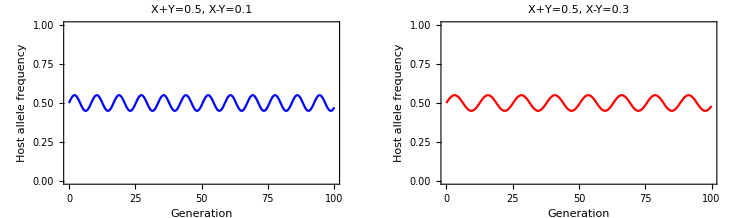

```mathematica
GraphicsRow[{Show[timePlotH[init1,paras1,Blue],PlotLabel-> "X+Y=0.5, X-Y=0.1",Frame-> True,FrameLabel-> {"Generation","Host allele frequency"}],Show[timePlotH[init1,paras2,Red],PlotLabel-> "X+Y=0.5, X-Y=0.3",Frame-> True,FrameLabel-> {"Generation","Host allele frequency"}]}]
```

### Equilibria-Perturbation Solution

```mathematica
equs={gH1[t],gH2[t],gP1[t],gP2[t]}//Factor (*Don't miss equilbria*);
```

Substitute Taylor series expression for parameters that are small (ϕ, ω).

```mathematica
Sum[ϕ[j] ϵ^j,{j,1,2}]
```

ϵ ϕ[1]+ϵ^2 ϕ[2]

```mathematica
equs2=Factor[equs/.{ϕ-> Sum[ϕ[j] ϵ^j,{j,1,2}],ω-> Sum[ω[j] ϵ^j,{j,1,2}],μ-> Sum[μ[j] ϵ^j,{j,1,2}],ν-> Sum[ν[j] ϵ^j,{j,1,2}],pH1[t]-> Sum[pH1[j] ϵ^j,{j,0,2}],pH2[t]-> Sum[pH2[j] ϵ^j,{j,0,2}],pP1[t]-> Sum[pP1[j] ϵ^j,{j,0,2}],pP2[t]-> Sum[pP2[j] ϵ^j,{j,0,2}]}];
```

Solve for frequencies that set all ODEs to zero.

```mathematica
Solve[(equs2/.ϵ-> 0)=={0,0,0,0},{pH1[0],pH2[0],pP1[0],pP2[0]}]//MatrixForm
FirstTerms=Solve[(equs2/.ϵ-> 0)=={0,0,0,0},{pH1[0],pH2[0],pP1[0],pP2[0]}];
```

(pH1[0]→0 | pH2[0]→0 | pP1[0]→0 | pP2[0]→0
pH1[0]→1 | pH2[0]→0 | pP1[0]→0 | pP2[0]→0
pH1[0]→0 | pH2[0]→1 | pP1[0]→0 | pP2[0]→0
pH1[0]→1 | pH2[0]→1 | pP1[0]→0 | pP2[0]→0
pH1[0]→1/2 | pH2[0]→0 | pP1[0]→1/2 | pP2[0]→0
pH1[0]→1/2 | pH2[0]→1 | pP1[0]→1/2 | pP2[0]→0
pH1[0]→0 | pH2[0]→0 | pP1[0]→1 | pP2[0]→0
pH1[0]→1 | pH2[0]→0 | pP1[0]→1 | pP2[0]→0
pH1[0]→0 | pH2[0]→1 | pP1[0]→1 | pP2[0]→0
pH1[0]→1 | pH2[0]→1 | pP1[0]→1 | pP2[0]→0
pH1[0]→0 | pH2[0]→1/2 | pP1[0]→0 | pP2[0]→1/2
pH1[0]→1 | pH2[0]→1/2 | pP1[0]→0 | pP2[0]→1/2
pH1[0]→1/2 | pH2[0]→1/2 | pP1[0]→1/2 | pP2[0]→1/2
pH1[0]→0 | pH2[0]→1/2 | pP1[0]→1 | pP2[0]→1/2
pH1[0]→1 | pH2[0]→1/2 | pP1[0]→1 | pP2[0]→1/2
pH1[0]→0 | pH2[0]→0 | pP1[0]→0 | pP2[0]→1
pH1[0]→1 | pH2[0]→0 | pP1[0]→0 | pP2[0]→1
pH1[0]→0 | pH2[0]→1 | pP1[0]→0 | pP2[0]→1
pH1[0]→1 | pH2[0]→1 | pP1[0]→0 | pP2[0]→1
pH1[0]→1/2 | pH2[0]→0 | pP1[0]→1/2 | pP2[0]→1
pH1[0]→1/2 | pH2[0]→1 | pP1[0]→1/2 | pP2[0]→1
pH1[0]→0 | pH2[0]→0 | pP1[0]→1 | pP2[0]→1
pH1[0]→1 | pH2[0]→0 | pP1[0]→1 | pP2[0]→1
pH1[0]→0 | pH2[0]→1 | pP1[0]→1 | pP2[0]→1
pH1[0]→1 | pH2[0]→1 | pP1[0]→1 | pP2[0]→1)

#### Equilibria 1: all fixed for WT allele

```mathematica
FirstTerms[[1]]
```

{pH1[0]→0,pH2[0]→0,pP1[0]→0,pP2[0]→0}

If at equilibrium and zeroth term works, then if the second order term also has to be zero at equilibrium

```mathematica
map=Map[D[#,ϵ]&,equs2];
```

```mathematica
SecondTerm[1]=Flatten[Solve[(map/.ϵ-> 0/.FirstTerms[[1]])=={0,0,0,0},{pH1[1],pH2[1],pP1[1],pP2[1]}]]
```

{pH1[1]→0,pH2[1]→0,pP1[1]→0,pP2[1]→0}

```mathematica
map2=Map[D[#,{ϵ,2}]&,equs2];
```

```mathematica
ThirdTerm[1]=Flatten[Solve[Normal[Series[Factor[equs2/.FirstTerms[[1]]/.SecondTerm[1]],{ϵ, 0,2}]]=={0,0,0,0},{pH1[2],pH2[2],pP1[2],pP2[2]}]]//Simplify
```

{pH1[2]→0,pH2[2]→0,pP1[2]→0,pP2[2]→0}

```mathematica
Normal[Series[equs2,{ϵ,0,2}]/.FirstTerms[[1]]/.SecondTerm[1]/.ThirdTerm[1]]//Factor
```

{0,0,0,0}

#### Equilibria 4: hosts fixed for mutant allele, parasites fixed for WT allele

```mathematica
FirstTerms[[4]]
```

{pH1[0]→1,pH2[0]→1,pP1[0]→0,pP2[0]→0}

If at equilibrium and zeroth term works, then if the second order term also has to be zero at equilibrium

```mathematica
map=Map[D[#,ϵ]&,equs2];
```

```mathematica
SecondTerm[4]=Flatten[Solve[(map/.ϵ-> 0/.FirstTerms[[4]])=={0,0,0,0},{pH1[1],pH2[1],pP1[1],pP2[1]}]]
```

{pH1[1]→0,pH2[1]→0,pP1[1]→0,pP2[1]→0}

```mathematica
map2=Map[D[#,{ϵ,2}]&,equs2];
```

```mathematica
ThirdTerm[4]=Flatten[Solve[Normal[Series[Factor[equs2/.FirstTerms[[4]]/.SecondTerm[4]],{ϵ, 0,2}]]=={0,0,0,0},{pH1[2],pH2[2],pP1[2],pP2[2]}]]
```

{pH1[2]→0,pH2[2]→0,pP1[2]→0,pP2[2]→0}

```mathematica
Normal[Series[equs2,{ϵ,0,2}]/.FirstTerms[[4]]/.SecondTerm[4]/.ThirdTerm[4]]//Factor
```

{0,0,0,0}

#### Equilibria 13: all polymorphic

```mathematica
FirstTerms[[13]]
```

{pH1[0]→1/2,pH2[0]→1/2,pP1[0]→1/2,pP2[0]→1/2}

Substitute in generating solution (i.e., solution to first term) to equations and take Taylor series approximation to second order:

```mathematica
Normal[Series[Factor[equs2/.FirstTerms[[13]]],{ϵ,0,1}]]
```

{(ϵ (-X α pP1[1]+Y α pP1[1]))/(X α+Y α+2 δ),(ϵ (-X α pP2[1]+Y α pP2[1]))/(X α+Y α+2 δ),(ϵ (X α pH1[1]-Y α pH1[1]))/(X α+Y α+2 δ),(ϵ (X α pH2[1]-Y α pH2[1]))/(X α+Y α+2 δ)}

If at equilibrium and zeroth term works, then the second term (first order) also has to be zero at equilibrium. Again substituting in the generating solution (i.e., solution to first term), solve such that the second term is also equal to zero:

```mathematica
SecondTerm[13]=Flatten[Solve[Normal[Series[Factor[equs2/.FirstTerms[[13]]],{ϵ,0,1}]]=={0,0,0,0},{pH1[1],pH2[1],pP1[1],pP2[1]}]]
```

{pH1[1]→0,pH2[1]→0,pP1[1]→0,pP2[1]→0}

Substituting in the solutions to the first and second terms (zeroth and first order, respecitvely), solve such that the third term (second order) is also equal to zero:

```mathematica
ThirdTerm[13]=Flatten[Solve[Normal[Series[Factor[equs2/.FirstTerms[[13]]/.SecondTerm[13]],{ϵ, 0,2}]]=={0,0,0,0},{pH1[2],pH2[2],pP1[2],pP2[2]}]]
```

{pH1[2]→0,pH2[2]→0,pP1[2]→0,pP2[2]→0}

```mathematica
Normal[Series[equs2,{ϵ,0,2}]/.FirstTerms[[13]]/.SecondTerm[13]/.ThirdTerm[13]]//Factor
```

{0,0,0,0}

#### Equilibria 22: hosts fixed for WT allele, parasites fixed for mutant allele

```mathematica
FirstTerms[[22]]
```

{pH1[0]→0,pH2[0]→0,pP1[0]→1,pP2[0]→1}

Substitute in generating solution (i.e., solution to first term) to equations and take Taylor series approximation to second order:

```mathematica
Normal[Series[Factor[equs2/.FirstTerms[[22]]],{ϵ,0,1}]]
```

{(ϵ (-X α pH1[1]+Y α pH1[1]))/(Y α+δ),(ϵ (-X α pH2[1]+Y α pH2[1]))/(Y α+δ),(ϵ (X α pP1[1]-Y α pP1[1]))/(Y α+δ),(ϵ (X α pP2[1]-Y α pP2[1]))/(Y α+δ)}

If at equilibrium and zeroth term works, then the second term (first order) also has to be zero at equilibrium. Again substituting in the generating solution (i.e., solution to first term), solve such that the second term is also equal to zero:

```mathematica
SecondTerm[22]=Flatten[Solve[Normal[Series[Factor[equs2/.FirstTerms[[22]]],{ϵ,0,1}]]=={0,0,0,0},{pH1[1],pH2[1],pP1[1],pP2[1]}]]
```

{pH1[1]→0,pH2[1]→0,pP1[1]→0,pP2[1]→0}

Substituting in the solutions to the first and second terms (zeroth and first order, respecitvely), solve such that the third term (second order) is also equal to zero:

```mathematica
ThirdTerm[22]=Flatten[Solve[Normal[Series[Factor[equs2/.FirstTerms[[22]]/.SecondTerm[22]],{ϵ, 0,2}]]=={0,0,0,0},{pH1[2],pH2[2],pP1[2],pP2[2]}]]
```

{pH1[2]→0,pH2[2]→0,pP1[2]→0,pP2[2]→0}

```mathematica
Normal[Series[equs2,{ϵ,0,2}]/.FirstTerms[[22]]/.SecondTerm[22]/.ThirdTerm[22]]//Factor
```

{0,0,0,0}

#### Equilibria 25: all fixed for mutant allele

```mathematica
FirstTerms[[25]]
```

{pH1[0]→1,pH2[0]→1,pP1[0]→1,pP2[0]→1}

Substitute in generating solution (i.e., solution to first term) to equations and take Taylor series approximation to second order:

```mathematica
Normal[Series[Factor[equs2/.FirstTerms[[25]]],{ϵ,0,1}]]
```

{(ϵ (X α pH1[1]-Y α pH1[1]))/(X α+δ),(ϵ (X α pH2[1]-Y α pH2[1]))/(X α+δ),(ϵ (-X α pP1[1]+Y α pP1[1]))/(X α+δ),(ϵ (-X α pP2[1]+Y α pP2[1]))/(X α+δ)}

If at equilibrium and zeroth term works, then the second term (first order) also has to be zero at equilibrium. Again substituting in the generating solution (i.e., solution to first term), solve such that the second term is also equal to zero:

```mathematica
SecondTerm[25]=Flatten[Solve[Normal[Series[Factor[equs2/.FirstTerms[[25]]],{ϵ,0,1}]]=={0,0,0,0},{pH1[1],pH2[1],pP1[1],pP2[1]}]]
```

{pH1[1]→0,pH2[1]→0,pP1[1]→0,pP2[1]→0}

Substituting in the solutions to the first and second terms (zeroth and first order, respecitvely), solve such that the third term (second order) is also equal to zero:

```mathematica
ThirdTerm[25]=Flatten[Solve[Normal[Series[Factor[equs2/.FirstTerms[[25]]/.SecondTerm[25]],{ϵ, 0,2}]]=={0,0,0,0},{pH1[2],pH2[2],pP1[2],pP2[2]}]]
```

{pH1[2]→0,pH2[2]→0,pP1[2]→0,pP2[2]→0}

```mathematica
Normal[Series[equs2,{ϵ,0,2}]/.FirstTerms[[25]]/.SecondTerm[25]/.ThirdTerm[25]]//Factor
```

{0,0,0,0}

### Stability-Perturbation Solution

If any eigenvalue has a positive real part, the system will tend to move away from the fixed point (unstable system).
If all eigenvalues have a negative real part, the system will tend to move back to steady state (stable system).
If any eigenvalue has an imaginary part, the system oscillate around the steady state.
If eigenvalue is zero, the system remains position or amplitude constant.

Set up Jacobian matrix.

```mathematica
Clear[jMtrx]
jMtrx={{D[gH1[t],pH1[t]],D[gH1[t],pH2[t]],D[gH1[t],pP1[t]],D[gH1[t],pP2[t]]},
{D[gH2[t],pH1[t]],D[gH2[t],pH2[t]],D[gH2[t],pP1[t]],D[gH2[t],pP2[t]]},
{D[gP1[t],pH1[t]],D[gP1[t],pH2[t]],D[gP1[t],pP1[t]],D[gP1[t],pP2[t]]},
{D[gP2[t],pH1[t]],D[gP2[t],pH2[t]],D[gP2[t],pP1[t]],D[gP2[t],pP2[t]]}};
```

Substitute in Taylor series approximations of migration and mutation rates and allele frequencies.

```mathematica
jMtrx2=jMtrx/.{ϕ-> Sum[ϕ[j] ϵ^j,{j,1,2}],ω-> Sum[ω[j] ϵ^j,{j,1,2}],μ-> Sum[μ[j] ϵ^j,{j,1,2}],ν-> Sum[ν[j] ϵ^j,{j,1,2}],pH1[t]-> Sum[pH1[j] ϵ^j,{j,0,2}],pH2[t]-> Sum[pH2[j] ϵ^j,{j,0,2}],pP1[t]-> Sum[pP1[j] ϵ^j,{j,0,2}],pP2[t]-> Sum[pP2[j] ϵ^j,{j,0,2}]};
```

Solve for the characteristic polynomial and substitution in Taylor series expansions for allele frequencies and mutation and migration rates:

```mathematica
ϵorder=3;
CP=CharacteristicPolynomial[jMtrx,λ]/.{ϕ-> Sum[ϕ[j] ϵ^j,{j,1,ϵorder}],ω-> Sum[ω[j] ϵ^j,{j,1,ϵorder}],μ-> Sum[μ[j] ϵ^j,{j,1,ϵorder}],ν-> Sum[ν[j] ϵ^j,{j,1,ϵorder}],pH1[t]-> Sum[pH1[j] ϵ^j,{j,0,ϵorder}],pH2[t]-> Sum[pH2[j] ϵ^j,{j,0,ϵorder}],pP1[t]-> Sum[pP1[j] ϵ^j,{j,0,ϵorder}],pP2[t]-> Sum[pP2[j] ϵ^j,{j,0,ϵorder}],λ-> Sum[λ[j] ϵ^j,{j,0,ϵorder}]};
```

```mathematica
λ0sol[e_]:=Simplify[Solve[(CP/.ϵ-> 0/.FirstTerms[[e]])==0,λ[0]],Assumptions->{X>0,Y>0,δ>0}]
```

```mathematica
Clear[λ1sol,λ1factor]
λ1factor[e_,o_]:=Table[Factor[D[CP,{ϵ,o}]/.ϵ->0/.FirstTerms[[13]]/.SecondTerm[13]/.ThirdTerm[13]/.λ0sol[13][[j]]],{j,1,4}];λ1sol[e_,o_]:=Table[Flatten[Solve[Factor[D[CP,{ϵ,o}]/.ϵ->0/.FirstTerms[[e]]/.SecondTerm[e]/.ThirdTerm[e]/.λ0sol[e][[j]]]==0,λ[1]]]//Simplify,{j,1,4}]
```

#### Equilibria 1: all fixed for WT allele

```mathematica
FirstTerms[[1]]
SecondTerm[1]
ThirdTerm[1]
```

{pH1[0]→0,pH2[0]→0,pP1[0]→0,pP2[0]→0}

{pH1[1]→0,pH2[1]→0,pP1[1]→0,pP2[1]→0}

{pH1[2]→0,pH2[2]→0,pP1[2]→0,pP2[2]→0}

```mathematica
λ0sol[1]//DeleteDuplicates
```

{{λ[0]→((X-Y) α)/(X α+δ)},{λ[0]→((-X+Y) α)/(X α+δ)}}

```mathematica
λ0sol[1][[1]]
λ0sol[1][[3]]
```

{λ[0]→((X-Y) α)/(X α+δ)}

{λ[0]→((-X+Y) α)/(X α+δ)}

```mathematica
λ1factor[1,1]
λ1factor[1,2]
```

{(4 ⅈ (X-Y)^3 α^3 (X α+Y α+2 δ-√((X α+Y α+2 δ)^2)) (X α+Y α+2 δ+√((X α+Y α+2 δ)^2)) (X α λ[1]+Y α λ[1]+2 δ λ[1]+ϕ[1]+ω[1]))/((X α+Y α+2 δ)^3 ((X α+Y α+2 δ)^2)^(3/2)),(4 ⅈ (X-Y)^3 α^3 (X α+Y α+2 δ-√((X α+Y α+2 δ)^2)) (X α+Y α+2 δ+√((X α+Y α+2 δ)^2)) (X α λ[1]+Y α λ[1]+2 δ λ[1]+ϕ[1]+ω[1]))/((X α+Y α+2 δ)^3 ((X α+Y α+2 δ)^2)^(3/2)),-((4 ⅈ (X-Y)^3 α^3 (X α+Y α+2 δ-√((X α+Y α+2 δ)^2)) (X α+Y α+2 δ+√((X α+Y α+2 δ)^2)) (X α λ[1]+Y α λ[1]+2 δ λ[1]+ϕ[1]+ω[1]))/((X α+Y α+2 δ)^3 ((X α+Y α+2 δ)^2)^(3/2))),-((4 ⅈ (X-Y)^3 α^3 (X α+Y α+2 δ-√((X α+Y α+2 δ)^2)) (X α+Y α+2 δ+√((X α+Y α+2 δ)^2)) (X α λ[1]+Y α λ[1]+2 δ λ[1]+ϕ[1]+ω[1]))/((X α+Y α+2 δ)^3 ((X α+Y α+2 δ)^2)^(3/2)))}

{1/(X α+Y α+2 δ)^6 4 (X-Y)^2 α^2 (-3 X^4 α^4 λ[1]^2-12 X^3 Y α^4 λ[1]^2-18 X^2 Y^2 α^4 λ[1]^2-12 X Y^3 α^4 λ[1]^2-3 Y^4 α^4 λ[1]^2-24 X^3 α^3 δ λ[1]^2-72 X^2 Y α^3 δ λ[1]^2-72 X Y^2 α^3 δ λ[1]^2-24 Y^3 α^3 δ λ[1]^2-72 X^2 α^2 δ^2 λ[1]^2-144 X Y α^2 δ^2 λ[1]^2-72 Y^2 α^2 δ^2 λ[1]^2-96 X α δ^3 λ[1]^2-96 Y α δ^3 λ[1]^2-48 δ^4 λ[1]^2+X^2 α^2 (X α+Y α+2 δ)^2 λ[1]^2+2 X Y α^2 (X α+Y α+2 δ)^2 λ[1]^2+Y^2 α^2 (X α+Y α+2 δ)^2 λ[1]^2+4 X α δ (X α+Y α+2 δ)^2 λ[1]^2+4 Y α δ (X α+Y α+2 δ)^2 λ[1]^2+4 δ^2 (X α+Y α+2 δ)^2 λ[1]^2-6 X^3 α^3 λ[1] ϕ[1]-18 X^2 Y α^3 λ[1] ϕ[1]-18 X Y^2 α^3 λ[1] ϕ[1]-6 Y^3 α^3 λ[1] ϕ[1]-36 X^2 α^2 δ λ[1] ϕ[1]-72 X Y α^2 δ λ[1] ϕ[1]-36 Y^2 α^2 δ λ[1] ϕ[1]-72 X α δ^2 λ[1] ϕ[1]-72 Y α δ^2 λ[1] ϕ[1]-48 δ^3 λ[1] ϕ[1]+2 X α (X α+Y α+2 δ)^2 λ[1] ϕ[1]+2 Y α (X α+Y α+2 δ)^2 λ[1] ϕ[1]+4 δ (X α+Y α+2 δ)^2 λ[1] ϕ[1]-6 X^3 α^3 λ[1] ω[1]-18 X^2 Y α^3 λ[1] ω[1]-18 X Y^2 α^3 λ[1] ω[1]-6 Y^3 α^3 λ[1] ω[1]-36 X^2 α^2 δ λ[1] ω[1]-72 X Y α^2 δ λ[1] ω[1]-36 Y^2 α^2 δ λ[1] ω[1]-72 X α δ^2 λ[1] ω[1]-72 Y α δ^2 λ[1] ω[1]-48 δ^3 λ[1] ω[1]+2 X α (X α+Y α+2 δ)^2 λ[1] ω[1]+2 Y α (X α+Y α+2 δ)^2 λ[1] ω[1]+4 δ (X α+Y α+2 δ)^2 λ[1] ω[1]-8 X^2 α^2 ϕ[1] ω[1]-16 X Y α^2 ϕ[1] ω[1]-8 Y^2 α^2 ϕ[1] ω[1]-32 X α δ ϕ[1] ω[1]-32 Y α δ ϕ[1] ω[1]-32 δ^2 ϕ[1] ω[1]+8 (X α+Y α+2 δ)^2 ϕ[1] ω[1]),1/(X α+Y α+2 δ)^6 4 (X-Y)^2 α^2 (-3 X^4 α^4 λ[1]^2-12 X^3 Y α^4 λ[1]^2-18 X^2 Y^2 α^4 λ[1]^2-12 X Y^3 α^4 λ[1]^2-3 Y^4 α^4 λ[1]^2-24 X^3 α^3 δ λ[1]^2-72 X^2 Y α^3 δ λ[1]^2-72 X Y^2 α^3 δ λ[1]^2-24 Y^3 α^3 δ λ[1]^2-72 X^2 α^2 δ^2 λ[1]^2-144 X Y α^2 δ^2 λ[1]^2-72 Y^2 α^2 δ^2 λ[1]^2-96 X α δ^3 λ[1]^2-96 Y α δ^3 λ[1]^2-48 δ^4 λ[1]^2+X^2 α^2 (X α+Y α+2 δ)^2 λ[1]^2+2 X Y α^2 (X α+Y α+2 δ)^2 λ[1]^2+Y^2 α^2 (X α+Y α+2 δ)^2 λ[1]^2+4 X α δ (X α+Y α+2 δ)^2 λ[1]^2+4 Y α δ (X α+Y α+2 δ)^2 λ[1]^2+4 δ^2 (X α+Y α+2 δ)^2 λ[1]^2-6 X^3 α^3 λ[1] ϕ[1]-18 X^2 Y α^3 λ[1] ϕ[1]-18 X Y^2 α^3 λ[1] ϕ[1]-6 Y^3 α^3 λ[1] ϕ[1]-36 X^2 α^2 δ λ[1] ϕ[1]-72 X Y α^2 δ λ[1] ϕ[1]-36 Y^2 α^2 δ λ[1] ϕ[1]-72 X α δ^2 λ[1] ϕ[1]-72 Y α δ^2 λ[1] ϕ[1]-48 δ^3 λ[1] ϕ[1]+2 X α (X α+Y α+2 δ)^2 λ[1] ϕ[1]+2 Y α (X α+Y α+2 δ)^2 λ[1] ϕ[1]+4 δ (X α+Y α+2 δ)^2 λ[1] ϕ[1]-6 X^3 α^3 λ[1] ω[1]-18 X^2 Y α^3 λ[1] ω[1]-18 X Y^2 α^3 λ[1] ω[1]-6 Y^3 α^3 λ[1] ω[1]-36 X^2 α^2 δ λ[1] ω[1]-72 X Y α^2 δ λ[1] ω[1]-36 Y^2 α^2 δ λ[1] ω[1]-72 X α δ^2 λ[1] ω[1]-72 Y α δ^2 λ[1] ω[1]-48 δ^3 λ[1] ω[1]+2 X α (X α+Y α+2 δ)^2 λ[1] ω[1]+2 Y α (X α+Y α+2 δ)^2 λ[1] ω[1]+4 δ (X α+Y α+2 δ)^2 λ[1] ω[1]-8 X^2 α^2 ϕ[1] ω[1]-16 X Y α^2 ϕ[1] ω[1]-8 Y^2 α^2 ϕ[1] ω[1]-32 X α δ ϕ[1] ω[1]-32 Y α δ ϕ[1] ω[1]-32 δ^2 ϕ[1] ω[1]+8 (X α+Y α+2 δ)^2 ϕ[1] ω[1]),1/(X α+Y α+2 δ)^6 4 (X-Y)^2 α^2 (-3 X^4 α^4 λ[1]^2-12 X^3 Y α^4 λ[1]^2-18 X^2 Y^2 α^4 λ[1]^2-12 X Y^3 α^4 λ[1]^2-3 Y^4 α^4 λ[1]^2-24 X^3 α^3 δ λ[1]^2-72 X^2 Y α^3 δ λ[1]^2-72 X Y^2 α^3 δ λ[1]^2-24 Y^3 α^3 δ λ[1]^2-72 X^2 α^2 δ^2 λ[1]^2-144 X Y α^2 δ^2 λ[1]^2-72 Y^2 α^2 δ^2 λ[1]^2-96 X α δ^3 λ[1]^2-96 Y α δ^3 λ[1]^2-48 δ^4 λ[1]^2+X^2 α^2 (X α+Y α+2 δ)^2 λ[1]^2+2 X Y α^2 (X α+Y α+2 δ)^2 λ[1]^2+Y^2 α^2 (X α+Y α+2 δ)^2 λ[1]^2+4 X α δ (X α+Y α+2 δ)^2 λ[1]^2+4 Y α δ (X α+Y α+2 δ)^2 λ[1]^2+4 δ^2 (X α+Y α+2 δ)^2 λ[1]^2-6 X^3 α^3 λ[1] ϕ[1]-18 X^2 Y α^3 λ[1] ϕ[1]-18 X Y^2 α^3 λ[1] ϕ[1]-6 Y^3 α^3 λ[1] ϕ[1]-36 X^2 α^2 δ λ[1] ϕ[1]-72 X Y α^2 δ λ[1] ϕ[1]-36 Y^2 α^2 δ λ[1] ϕ[1]-72 X α δ^2 λ[1] ϕ[1]-72 Y α δ^2 λ[1] ϕ[1]-48 δ^3 λ[1] ϕ[1]+2 X α (X α+Y α+2 δ)^2 λ[1] ϕ[1]+2 Y α (X α+Y α+2 δ)^2 λ[1] ϕ[1]+4 δ (X α+Y α+2 δ)^2 λ[1] ϕ[1]-6 X^3 α^3 λ[1] ω[1]-18 X^2 Y α^3 λ[1] ω[1]-18 X Y^2 α^3 λ[1] ω[1]-6 Y^3 α^3 λ[1] ω[1]-36 X^2 α^2 δ λ[1] ω[1]-72 X Y α^2 δ λ[1] ω[1]-36 Y^2 α^2 δ λ[1] ω[1]-72 X α δ^2 λ[1] ω[1]-72 Y α δ^2 λ[1] ω[1]-48 δ^3 λ[1] ω[1]+2 X α (X α+Y α+2 δ)^2 λ[1] ω[1]+2 Y α (X α+Y α+2 δ)^2 λ[1] ω[1]+4 δ (X α+Y α+2 δ)^2 λ[1] ω[1]-8 X^2 α^2 ϕ[1] ω[1]-16 X Y α^2 ϕ[1] ω[1]-8 Y^2 α^2 ϕ[1] ω[1]-32 X α δ ϕ[1] ω[1]-32 Y α δ ϕ[1] ω[1]-32 δ^2 ϕ[1] ω[1]+8 (X α+Y α+2 δ)^2 ϕ[1] ω[1]),1/(X α+Y α+2 δ)^6 4 (X-Y)^2 α^2 (-3 X^4 α^4 λ[1]^2-12 X^3 Y α^4 λ[1]^2-18 X^2 Y^2 α^4 λ[1]^2-12 X Y^3 α^4 λ[1]^2-3 Y^4 α^4 λ[1]^2-24 X^3 α^3 δ λ[1]^2-72 X^2 Y α^3 δ λ[1]^2-72 X Y^2 α^3 δ λ[1]^2-24 Y^3 α^3 δ λ[1]^2-72 X^2 α^2 δ^2 λ[1]^2-144 X Y α^2 δ^2 λ[1]^2-72 Y^2 α^2 δ^2 λ[1]^2-96 X α δ^3 λ[1]^2-96 Y α δ^3 λ[1]^2-48 δ^4 λ[1]^2+X^2 α^2 (X α+Y α+2 δ)^2 λ[1]^2+2 X Y α^2 (X α+Y α+2 δ)^2 λ[1]^2+Y^2 α^2 (X α+Y α+2 δ)^2 λ[1]^2+4 X α δ (X α+Y α+2 δ)^2 λ[1]^2+4 Y α δ (X α+Y α+2 δ)^2 λ[1]^2+4 δ^2 (X α+Y α+2 δ)^2 λ[1]^2-6 X^3 α^3 λ[1] ϕ[1]-18 X^2 Y α^3 λ[1] ϕ[1]-18 X Y^2 α^3 λ[1] ϕ[1]-6 Y^3 α^3 λ[1] ϕ[1]-36 X^2 α^2 δ λ[1] ϕ[1]-72 X Y α^2 δ λ[1] ϕ[1]-36 Y^2 α^2 δ λ[1] ϕ[1]-72 X α δ^2 λ[1] ϕ[1]-72 Y α δ^2 λ[1] ϕ[1]-48 δ^3 λ[1] ϕ[1]+2 X α (X α+Y α+2 δ)^2 λ[1] ϕ[1]+2 Y α (X α+Y α+2 δ)^2 λ[1] ϕ[1]+4 δ (X α+Y α+2 δ)^2 λ[1] ϕ[1]-6 X^3 α^3 λ[1] ω[1]-18 X^2 Y α^3 λ[1] ω[1]-18 X Y^2 α^3 λ[1] ω[1]-6 Y^3 α^3 λ[1] ω[1]-36 X^2 α^2 δ λ[1] ω[1]-72 X Y α^2 δ λ[1] ω[1]-36 Y^2 α^2 δ λ[1] ω[1]-72 X α δ^2 λ[1] ω[1]-72 Y α δ^2 λ[1] ω[1]-48 δ^3 λ[1] ω[1]+2 X α (X α+Y α+2 δ)^2 λ[1] ω[1]+2 Y α (X α+Y α+2 δ)^2 λ[1] ω[1]+4 δ (X α+Y α+2 δ)^2 λ[1] ω[1]-8 X^2 α^2 ϕ[1] ω[1]-16 X Y α^2 ϕ[1] ω[1]-8 Y^2 α^2 ϕ[1] ω[1]-32 X α δ ϕ[1] ω[1]-32 Y α δ ϕ[1] ω[1]-32 δ^2 ϕ[1] ω[1]+8 (X α+Y α+2 δ)^2 ϕ[1] ω[1])}

```mathematica
λ1sol[1,2][[1]]/.μ[1]-> 0/.ν[1]-> 0//Simplify
λ1sol[1,2][[3]]/.μ[1]-> 0/.ν[1]-> 0//Simplify
```

{λ[1]→0,λ[1]→-(2 ϕ[1])/(X α+δ)}

{λ[1]→0,λ[1]→-(2 ω[1])/(X α+δ)}

#### Equilibria 4: hosts fixed for mutant allele, parasites fixed for WT allele

```mathematica
FirstTerms[[4]]
SecondTerm[4]
ThirdTerm[4]
```

{pH1[0]→1,pH2[0]→1,pP1[0]→0,pP2[0]→0}

{pH1[1]→0,pH2[1]→0,pP1[1]→0,pP2[1]→0}

{pH1[2]→0,pH2[2]→0,pP1[2]→0,pP2[2]→0}

```mathematica
λ0sol[4]//DeleteDuplicates
```

{{λ[0]→((X-Y) α)/(Y α+δ)},{λ[0]→((-X+Y) α)/(Y α+δ)}}

```mathematica
λ0sol[4][[1]]
λ0sol[4][[3]]
```

{λ[0]→((X-Y) α)/(Y α+δ)}

{λ[0]→((-X+Y) α)/(Y α+δ)}

```mathematica
λ1factor[4,1];
λ1factor[4,2];
```

```mathematica
λ1sol[4,2][[1]]
λ1sol[4,2][[3]]
```

{λ[1]→0,λ[1]→-(2 ω[1])/(Y α+δ)}

{λ[1]→0,λ[1]→-(2 ϕ[1])/(Y α+δ)}

#### Equilibria 13: all polymorphic

```mathematica
FirstTerms[[13]]
SecondTerm[13]
ThirdTerm[13]
```

{pH1[0]→1/2,pH2[0]→1/2,pP1[0]→1/2,pP2[0]→1/2}

{pH1[1]→0,pH2[1]→0,pP1[1]→0,pP2[1]→0}

{pH1[2]→0,pH2[2]→0,pP1[2]→0,pP2[2]→0}

```mathematica
λ0sol[13]//DeleteDuplicates
```

{{λ[0]→-(ⅈ (X-Y) α)/(√((X α+Y α+2 δ)^2))},{λ[0]→(ⅈ (X-Y) α)/(√((X α+Y α+2 δ)^2))}}

```mathematica
λ0sol[13][[1]]
λ0sol[13][[3]]
```

{λ[0]→-(ⅈ (X-Y) α)/(√((X α+Y α+2 δ)^2))}

{λ[0]→(ⅈ (X-Y) α)/(√((X α+Y α+2 δ)^2))}

```mathematica
λ1factor[13,1];
λ1factor[13,2];
```

```mathematica
λ1sol[13,2][[1]]
λ1sol[13,2][[3]]
```

{λ[1]→0,λ[1]→-(2 (ϕ[1]+ω[1]))/(X α+Y α+2 δ)}

{λ[1]→0,λ[1]→-(2 (ϕ[1]+ω[1]))/(X α+Y α+2 δ)}

There are four eigenvalues:
-(2 (μ[1]+ν[1]))/(X+Y+2 δ)±(ⅈ (X-Y))/(X+Y+2 δ)
-(2 (μ[1]+ν[1]+ϕ[1]+ω[1]))/(X+Y+2 δ)±(ⅈ (X-Y))/(X+Y+2 δ)

```mathematica
-(2 (μ[1]+ν[1]))/(X+Y+2 δ)
```

#### Equilibria 22: hosts fixed for WT allele, parasites fixed for mutant allele

```mathematica
FirstTerms[[22]]
SecondTerm[22]
ThirdTerm[22]
```

{pH1[0]→0,pH2[0]→0,pP1[0]→1,pP2[0]→1}

{pH1[1]→0,pH2[1]→0,pP1[1]→0,pP2[1]→0}

{pH1[2]→0,pH2[2]→0,pP1[2]→0,pP2[2]→0}

```mathematica
λ0sol[22]//DeleteDuplicates
```

{{λ[0]→((X-Y) α)/(Y α+δ)},{λ[0]→((-X+Y) α)/(Y α+δ)}}

```mathematica
λ0sol[22][[1]]
λ0sol[22][[3]]
```

{λ[0]→((X-Y) α)/(Y α+δ)}

{λ[0]→((-X+Y) α)/(Y α+δ)}

```mathematica
λ1factor[22,1];
λ1factor[22,2];
```

{(4 ⅈ (X-Y)^3 α^3 (X α+Y α+2 δ-√((X α+Y α+2 δ)^2)) (X α+Y α+2 δ+√((X α+Y α+2 δ)^2)) (X α λ[1]+Y α λ[1]+2 δ λ[1]+ϕ[1]+ω[1]))/((X α+Y α+2 δ)^3 ((X α+Y α+2 δ)^2)^(3/2)),(4 ⅈ (X-Y)^3 α^3 (X α+Y α+2 δ-√((X α+Y α+2 δ)^2)) (X α+Y α+2 δ+√((X α+Y α+2 δ)^2)) (X α λ[1]+Y α λ[1]+2 δ λ[1]+ϕ[1]+ω[1]))/((X α+Y α+2 δ)^3 ((X α+Y α+2 δ)^2)^(3/2)),-((4 ⅈ (X-Y)^3 α^3 (X α+Y α+2 δ-√((X α+Y α+2 δ)^2)) (X α+Y α+2 δ+√((X α+Y α+2 δ)^2)) (X α λ[1]+Y α λ[1]+2 δ λ[1]+ϕ[1]+ω[1]))/((X α+Y α+2 δ)^3 ((X α+Y α+2 δ)^2)^(3/2))),-((4 ⅈ (X-Y)^3 α^3 (X α+Y α+2 δ-√((X α+Y α+2 δ)^2)) (X α+Y α+2 δ+√((X α+Y α+2 δ)^2)) (X α λ[1]+Y α λ[1]+2 δ λ[1]+ϕ[1]+ω[1]))/((X α+Y α+2 δ)^3 ((X α+Y α+2 δ)^2)^(3/2)))}

{1/(X α+Y α+2 δ)^6 4 (X-Y)^2 α^2 (-3 X^4 α^4 λ[1]^2-12 X^3 Y α^4 λ[1]^2-18 X^2 Y^2 α^4 λ[1]^2-12 X Y^3 α^4 λ[1]^2-3 Y^4 α^4 λ[1]^2-24 X^3 α^3 δ λ[1]^2-72 X^2 Y α^3 δ λ[1]^2-72 X Y^2 α^3 δ λ[1]^2-24 Y^3 α^3 δ λ[1]^2-72 X^2 α^2 δ^2 λ[1]^2-144 X Y α^2 δ^2 λ[1]^2-72 Y^2 α^2 δ^2 λ[1]^2-96 X α δ^3 λ[1]^2-96 Y α δ^3 λ[1]^2-48 δ^4 λ[1]^2+X^2 α^2 (X α+Y α+2 δ)^2 λ[1]^2+2 X Y α^2 (X α+Y α+2 δ)^2 λ[1]^2+Y^2 α^2 (X α+Y α+2 δ)^2 λ[1]^2+4 X α δ (X α+Y α+2 δ)^2 λ[1]^2+4 Y α δ (X α+Y α+2 δ)^2 λ[1]^2+4 δ^2 (X α+Y α+2 δ)^2 λ[1]^2-6 X^3 α^3 λ[1] ϕ[1]-18 X^2 Y α^3 λ[1] ϕ[1]-18 X Y^2 α^3 λ[1] ϕ[1]-6 Y^3 α^3 λ[1] ϕ[1]-36 X^2 α^2 δ λ[1] ϕ[1]-72 X Y α^2 δ λ[1] ϕ[1]-36 Y^2 α^2 δ λ[1] ϕ[1]-72 X α δ^2 λ[1] ϕ[1]-72 Y α δ^2 λ[1] ϕ[1]-48 δ^3 λ[1] ϕ[1]+2 X α (X α+Y α+2 δ)^2 λ[1] ϕ[1]+2 Y α (X α+Y α+2 δ)^2 λ[1] ϕ[1]+4 δ (X α+Y α+2 δ)^2 λ[1] ϕ[1]-6 X^3 α^3 λ[1] ω[1]-18 X^2 Y α^3 λ[1] ω[1]-18 X Y^2 α^3 λ[1] ω[1]-6 Y^3 α^3 λ[1] ω[1]-36 X^2 α^2 δ λ[1] ω[1]-72 X Y α^2 δ λ[1] ω[1]-36 Y^2 α^2 δ λ[1] ω[1]-72 X α δ^2 λ[1] ω[1]-72 Y α δ^2 λ[1] ω[1]-48 δ^3 λ[1] ω[1]+2 X α (X α+Y α+2 δ)^2 λ[1] ω[1]+2 Y α (X α+Y α+2 δ)^2 λ[1] ω[1]+4 δ (X α+Y α+2 δ)^2 λ[1] ω[1]-8 X^2 α^2 ϕ[1] ω[1]-16 X Y α^2 ϕ[1] ω[1]-8 Y^2 α^2 ϕ[1] ω[1]-32 X α δ ϕ[1] ω[1]-32 Y α δ ϕ[1] ω[1]-32 δ^2 ϕ[1] ω[1]+8 (X α+Y α+2 δ)^2 ϕ[1] ω[1]),1/(X α+Y α+2 δ)^6 4 (X-Y)^2 α^2 (-3 X^4 α^4 λ[1]^2-12 X^3 Y α^4 λ[1]^2-18 X^2 Y^2 α^4 λ[1]^2-12 X Y^3 α^4 λ[1]^2-3 Y^4 α^4 λ[1]^2-24 X^3 α^3 δ λ[1]^2-72 X^2 Y α^3 δ λ[1]^2-72 X Y^2 α^3 δ λ[1]^2-24 Y^3 α^3 δ λ[1]^2-72 X^2 α^2 δ^2 λ[1]^2-144 X Y α^2 δ^2 λ[1]^2-72 Y^2 α^2 δ^2 λ[1]^2-96 X α δ^3 λ[1]^2-96 Y α δ^3 λ[1]^2-48 δ^4 λ[1]^2+X^2 α^2 (X α+Y α+2 δ)^2 λ[1]^2+2 X Y α^2 (X α+Y α+2 δ)^2 λ[1]^2+Y^2 α^2 (X α+Y α+2 δ)^2 λ[1]^2+4 X α δ (X α+Y α+2 δ)^2 λ[1]^2+4 Y α δ (X α+Y α+2 δ)^2 λ[1]^2+4 δ^2 (X α+Y α+2 δ)^2 λ[1]^2-6 X^3 α^3 λ[1] ϕ[1]-18 X^2 Y α^3 λ[1] ϕ[1]-18 X Y^2 α^3 λ[1] ϕ[1]-6 Y^3 α^3 λ[1] ϕ[1]-36 X^2 α^2 δ λ[1] ϕ[1]-72 X Y α^2 δ λ[1] ϕ[1]-36 Y^2 α^2 δ λ[1] ϕ[1]-72 X α δ^2 λ[1] ϕ[1]-72 Y α δ^2 λ[1] ϕ[1]-48 δ^3 λ[1] ϕ[1]+2 X α (X α+Y α+2 δ)^2 λ[1] ϕ[1]+2 Y α (X α+Y α+2 δ)^2 λ[1] ϕ[1]+4 δ (X α+Y α+2 δ)^2 λ[1] ϕ[1]-6 X^3 α^3 λ[1] ω[1]-18 X^2 Y α^3 λ[1] ω[1]-18 X Y^2 α^3 λ[1] ω[1]-6 Y^3 α^3 λ[1] ω[1]-36 X^2 α^2 δ λ[1] ω[1]-72 X Y α^2 δ λ[1] ω[1]-36 Y^2 α^2 δ λ[1] ω[1]-72 X α δ^2 λ[1] ω[1]-72 Y α δ^2 λ[1] ω[1]-48 δ^3 λ[1] ω[1]+2 X α (X α+Y α+2 δ)^2 λ[1] ω[1]+2 Y α (X α+Y α+2 δ)^2 λ[1] ω[1]+4 δ (X α+Y α+2 δ)^2 λ[1] ω[1]-8 X^2 α^2 ϕ[1] ω[1]-16 X Y α^2 ϕ[1] ω[1]-8 Y^2 α^2 ϕ[1] ω[1]-32 X α δ ϕ[1] ω[1]-32 Y α δ ϕ[1] ω[1]-32 δ^2 ϕ[1] ω[1]+8 (X α+Y α+2 δ)^2 ϕ[1] ω[1]),1/(X α+Y α+2 δ)^6 4 (X-Y)^2 α^2 (-3 X^4 α^4 λ[1]^2-12 X^3 Y α^4 λ[1]^2-18 X^2 Y^2 α^4 λ[1]^2-12 X Y^3 α^4 λ[1]^2-3 Y^4 α^4 λ[1]^2-24 X^3 α^3 δ λ[1]^2-72 X^2 Y α^3 δ λ[1]^2-72 X Y^2 α^3 δ λ[1]^2-24 Y^3 α^3 δ λ[1]^2-72 X^2 α^2 δ^2 λ[1]^2-144 X Y α^2 δ^2 λ[1]^2-72 Y^2 α^2 δ^2 λ[1]^2-96 X α δ^3 λ[1]^2-96 Y α δ^3 λ[1]^2-48 δ^4 λ[1]^2+X^2 α^2 (X α+Y α+2 δ)^2 λ[1]^2+2 X Y α^2 (X α+Y α+2 δ)^2 λ[1]^2+Y^2 α^2 (X α+Y α+2 δ)^2 λ[1]^2+4 X α δ (X α+Y α+2 δ)^2 λ[1]^2+4 Y α δ (X α+Y α+2 δ)^2 λ[1]^2+4 δ^2 (X α+Y α+2 δ)^2 λ[1]^2-6 X^3 α^3 λ[1] ϕ[1]-18 X^2 Y α^3 λ[1] ϕ[1]-18 X Y^2 α^3 λ[1] ϕ[1]-6 Y^3 α^3 λ[1] ϕ[1]-36 X^2 α^2 δ λ[1] ϕ[1]-72 X Y α^2 δ λ[1] ϕ[1]-36 Y^2 α^2 δ λ[1] ϕ[1]-72 X α δ^2 λ[1] ϕ[1]-72 Y α δ^2 λ[1] ϕ[1]-48 δ^3 λ[1] ϕ[1]+2 X α (X α+Y α+2 δ)^2 λ[1] ϕ[1]+2 Y α (X α+Y α+2 δ)^2 λ[1] ϕ[1]+4 δ (X α+Y α+2 δ)^2 λ[1] ϕ[1]-6 X^3 α^3 λ[1] ω[1]-18 X^2 Y α^3 λ[1] ω[1]-18 X Y^2 α^3 λ[1] ω[1]-6 Y^3 α^3 λ[1] ω[1]-36 X^2 α^2 δ λ[1] ω[1]-72 X Y α^2 δ λ[1] ω[1]-36 Y^2 α^2 δ λ[1] ω[1]-72 X α δ^2 λ[1] ω[1]-72 Y α δ^2 λ[1] ω[1]-48 δ^3 λ[1] ω[1]+2 X α (X α+Y α+2 δ)^2 λ[1] ω[1]+2 Y α (X α+Y α+2 δ)^2 λ[1] ω[1]+4 δ (X α+Y α+2 δ)^2 λ[1] ω[1]-8 X^2 α^2 ϕ[1] ω[1]-16 X Y α^2 ϕ[1] ω[1]-8 Y^2 α^2 ϕ[1] ω[1]-32 X α δ ϕ[1] ω[1]-32 Y α δ ϕ[1] ω[1]-32 δ^2 ϕ[1] ω[1]+8 (X α+Y α+2 δ)^2 ϕ[1] ω[1]),1/(X α+Y α+2 δ)^6 4 (X-Y)^2 α^2 (-3 X^4 α^4 λ[1]^2-12 X^3 Y α^4 λ[1]^2-18 X^2 Y^2 α^4 λ[1]^2-12 X Y^3 α^4 λ[1]^2-3 Y^4 α^4 λ[1]^2-24 X^3 α^3 δ λ[1]^2-72 X^2 Y α^3 δ λ[1]^2-72 X Y^2 α^3 δ λ[1]^2-24 Y^3 α^3 δ λ[1]^2-72 X^2 α^2 δ^2 λ[1]^2-144 X Y α^2 δ^2 λ[1]^2-72 Y^2 α^2 δ^2 λ[1]^2-96 X α δ^3 λ[1]^2-96 Y α δ^3 λ[1]^2-48 δ^4 λ[1]^2+X^2 α^2 (X α+Y α+2 δ)^2 λ[1]^2+2 X Y α^2 (X α+Y α+2 δ)^2 λ[1]^2+Y^2 α^2 (X α+Y α+2 δ)^2 λ[1]^2+4 X α δ (X α+Y α+2 δ)^2 λ[1]^2+4 Y α δ (X α+Y α+2 δ)^2 λ[1]^2+4 δ^2 (X α+Y α+2 δ)^2 λ[1]^2-6 X^3 α^3 λ[1] ϕ[1]-18 X^2 Y α^3 λ[1] ϕ[1]-18 X Y^2 α^3 λ[1] ϕ[1]-6 Y^3 α^3 λ[1] ϕ[1]-36 X^2 α^2 δ λ[1] ϕ[1]-72 X Y α^2 δ λ[1] ϕ[1]-36 Y^2 α^2 δ λ[1] ϕ[1]-72 X α δ^2 λ[1] ϕ[1]-72 Y α δ^2 λ[1] ϕ[1]-48 δ^3 λ[1] ϕ[1]+2 X α (X α+Y α+2 δ)^2 λ[1] ϕ[1]+2 Y α (X α+Y α+2 δ)^2 λ[1] ϕ[1]+4 δ (X α+Y α+2 δ)^2 λ[1] ϕ[1]-6 X^3 α^3 λ[1] ω[1]-18 X^2 Y α^3 λ[1] ω[1]-18 X Y^2 α^3 λ[1] ω[1]-6 Y^3 α^3 λ[1] ω[1]-36 X^2 α^2 δ λ[1] ω[1]-72 X Y α^2 δ λ[1] ω[1]-36 Y^2 α^2 δ λ[1] ω[1]-72 X α δ^2 λ[1] ω[1]-72 Y α δ^2 λ[1] ω[1]-48 δ^3 λ[1] ω[1]+2 X α (X α+Y α+2 δ)^2 λ[1] ω[1]+2 Y α (X α+Y α+2 δ)^2 λ[1] ω[1]+4 δ (X α+Y α+2 δ)^2 λ[1] ω[1]-8 X^2 α^2 ϕ[1] ω[1]-16 X Y α^2 ϕ[1] ω[1]-8 Y^2 α^2 ϕ[1] ω[1]-32 X α δ ϕ[1] ω[1]-32 Y α δ ϕ[1] ω[1]-32 δ^2 ϕ[1] ω[1]+8 (X α+Y α+2 δ)^2 ϕ[1] ω[1])}

```mathematica
λ1sol[22,2][[1]]//Simplify
λ1sol[22,2][[3]]//Simplify
```

{λ[1]→0,λ[1]→-(2 ω[1])/(Y α+δ)}

{λ[1]→0,λ[1]→-(2 ϕ[1])/(Y α+δ)}

#### Equilibria 25: all fixed for mutant allele

```mathematica
FirstTerms[[25]]
SecondTerm[25]
ThirdTerm[25]
```

{pH1[0]→1,pH2[0]→1,pP1[0]→1,pP2[0]→1}

{pH1[1]→0,pH2[1]→0,pP1[1]→0,pP2[1]→0}

{pH1[2]→0,pH2[2]→0,pP1[2]→0,pP2[2]→0}

```mathematica
λ0sol[25]//DeleteDuplicates
```

{{λ[0]→((X-Y) α)/(X α+δ)},{λ[0]→((-X+Y) α)/(X α+δ)}}

```mathematica
λ0sol[25][[1]]
λ0sol[25][[3]]
```

{λ[0]→((X-Y) α)/(X α+δ)}

{λ[0]→((-X+Y) α)/(X α+δ)}

```mathematica
λ1factor[25,1];
λ1factor[25,2];
```

```mathematica
λ1sol[25,2][[1]]
λ1sol[25,2][[3]]
```

{λ[1]→0,λ[1]→-(2 ϕ[1])/(X α+δ)}

{λ[1]→0,λ[1]→-(2 ω[1])/(X α+δ)}

### Equilibria solution with migration

```mathematica
equs={gH1[t],gH2[t],gP1[t],gP2[t]}//Factor (*Don't miss equilbria*);
```

Substitute Taylor series expression for parameters that are small (ϕ, ω).

```mathematica
Sum[ϕ[j] ϵ^j,{j,1,2}]
```

ϵ ϕ[1]+ϵ^2 ϕ[2]

```mathematica
equs2=Factor[equs/.{ϕ-> Sum[ϕ[j] ϵ^j,{j,0,2}],ω-> Sum[ω[j] ϵ^j,{j,0,2}],μ-> Sum[μ[j] ϵ^j,{j,1,2}],ν-> Sum[ν[j] ϵ^j,{j,1,2}],pH1[t]-> Sum[pH1[j] ϵ^j,{j,0,2}],pH2[t]-> Sum[pH2[j] ϵ^j,{j,0,2}],pP1[t]-> Sum[pP1[j] ϵ^j,{j,0,2}],pP2[t]-> Sum[pP2[j] ϵ^j,{j,0,2}]}];
```

Solve for frequencies that set all ODEs to zero.

```mathematica
Solve[(equs2/.ϵ-> 0)=={0,0,0,0},{pH1[0],pH2[0],pP1[0],pP2[0]}]//MatrixForm
FirstTerms=Solve[(equs2/.ϵ-> 0)=={0,0,0,0},{pH1[0],pH2[0],pP1[0],pP2[0]}];
```

$Aborted

$Aborted

## Simulations

```mathematica
Clear[pars1, pars2,pars3,κscale,βSub]
pars1={κ->300*0.5,δ->0.5,γ-> 0.5,X-> 0.7,Y-> 0.1,α->1,τMax-> 100,ϕ-> 0.05,ω-> 0.05,fp-> 1};
pars2={κ->300*0.5,δ->0.5,γ-> 0.5,X-> 0.7,Y-> 0.1,α->1,τMax-> 100,ϕ-> 0.01,ω-> 0.01,fp-> 1};
pars3={κ->300*0.5,δ->0.5,γ-> 0.5,X-> 0.7,Y-> 0.1,α->1,τMax-> 100,ϕ-> 0.001,ω-> 0.001,fp-> 1};
pars1N={κ->300*0.5,δ->0.5,γ-> 0.5,X-> 0.4,Y-> 0.4,α->1,τMax-> 100,ϕ-> 0.05,ω-> 0.05,fp-> 1};
pars2N={κ->300*0.5,δ->0.5,γ-> 0.5,X-> 0.4,Y-> 0.4,α->1,τMax-> 100,ϕ-> 0.01,ω-> 0.01,fp-> 1};
pars3N={κ->300*0.5,δ->0.5,γ-> 0.5,X-> 0.4,Y-> 0.4,α->1,τMax-> 100,ϕ-> 0.001,ω-> 0.001,fp-> 1};
(*Parameters for scaling κ in different populations*)
κscale={1,1};
(*Transmission rates*)
βSub={β[1,1,1]->X/(κ*κscale[[1]]),β[1,2,1]->Y/(κ*κscale[[1]]),β[2,1,1]->Y/(κ*κscale[[1]]),β[2,2,1]->X/(κ*κscale[[1]]),β[1,1,2]->X/(κ*κscale[[2]]),β[1,2,2]->Y/(κ*κscale[[2]]),β[2,1,2]->Y/(κ*κscale[[2]]),β[2,2,2]->X/(κ*κscale[[2]])};
```

### Event matrix

The change in counts for each event.

```mathematica
Clear[ΔE]
ΔE=Block[{out},
H11={};
H12={};
P11={};
P12={};
(*Host turnover in population 1, 1-4*)
AppendTo[H11,Table[{If[i==k,0,If[i==1,-1,1]]},{i,1,2},{k,1,2}]];
AppendTo[P11,Table[{If[i==k,0,If[i==1,0,0]]},{i,1,2},{k,1,2}]];
AppendTo[H12,Table[{If[i==k,0,If[i==1,0,0]]},{i,1,2},{k,1,2}]];
AppendTo[P12,Table[{If[i==k,0,If[i==1,0,0]]},{i,1,2},{k,1,2}]];

(*Parasite turnover in population 1, 5-8*)
AppendTo[H11,Table[{If[j==l,0,If[j==1,0,0]]},{j,1,2},{l,1,2}]];
AppendTo[P11,Table[{If[j==l,0,If[j==1,-1,1]]},{j,1,2},{l,1,2}]];
AppendTo[H12,Table[{If[j==l,0,If[j==1,0,0]]},{j,1,2},{l,1,2}]];
AppendTo[P12,Table[{If[j==l,0,If[j==1,0,0]]},{j,1,2},{l,1,2}]];

(*Infection in population 1, 9-24*)
AppendTo[H11,Table[{If[i==k,0,If[i==1,-1,1]]},{i,1,2},{j,1,2},{k,1,2},{l,1,2}]];
AppendTo[P11,Table[{If[j==l,0,If[j==1,1,-1]]},{i,1,2},{j,1,2},{k,1,2},{l,1,2}]];
AppendTo[H12,Table[{If[i==k,0,If[i==1,0,0]]},{i,1,2},{j,1,2},{k,1,2},{l,1,2}]];
AppendTo[P12,Table[{If[j==l,0,If[j==1,0,0]]},{i,1,2},{j,1,2},{k,1,2},{l,1,2}]];

(*Host migration from population 1, 25-32*)
(*i is host that migrates out of pop 1, k is host that is born to replace and m is host that dies in pop 2*)
AppendTo[H11,Table[{If[i==k,0,If[i==1,-1,1]]},{i,1,2},{k,1,2},{m,1,2}]];
AppendTo[P11,Table[{If[i==k,0,If[i==1,0,0]]},{i,1,2},{k,1,2},{m,1,2}]];
AppendTo[H12,Table[{If[i==m,0,If[i==1,1,-1]]},{i,1,2},{k,1,2},{m,1,2}]];
AppendTo[P12,Table[{If[i==k,0,If[i==1,0,0]]},{i,1,2},{k,1,2},{m,1,2}]];

(*Parasite migration from population 1, 33-40*)
AppendTo[H11,Table[{If[i==k,0,If[i==1,0,0]]},{i,1,2},{k,1,2},{n,1,2}]];
AppendTo[P11,Table[{If[i==k,0,If[i==1,-1,1]]},{i,1,2},{k,1,2},{n,1,2}]];
AppendTo[H12,Table[{If[i==k,0,If[i==1,0,0]]},{i,1,2},{k,1,2},{n,1,2}]];
AppendTo[P12,Table[{If[i==n,0,If[i==1,1,-1]]},{i,1,2},{k,1,2},{n,1,2}]];

(*Host turnover in population 2, 41-44*)
AppendTo[H11,Table[{If[i==k,0,If[i==1,0,0]]},{i,1,2},{k,1,2}]];
AppendTo[P11,Table[{If[i==k,0,If[i==1,0,0]]},{i,1,2},{k,1,2}]];
AppendTo[H12,Table[{If[i==k,0,If[i==1,-1,1]]},{i,1,2},{k,1,2}]];
AppendTo[P12,Table[{If[i==k,0,If[i==1,0,0]]},{i,1,2},{k,1,2}]];

(*Parasite turnover in population 2, 45-48*)
AppendTo[H11,Table[{If[j==l,0,If[j==1,0,0]]},{j,1,2},{l,1,2}]];
AppendTo[P11,Table[{If[j==l,0,If[j==1,0,0]]},{j,1,2},{l,1,2}]];
AppendTo[H12,Table[{If[j==l,0,If[j==1,0,0]]},{j,1,2},{l,1,2}]];
AppendTo[P12,Table[{If[j==l,0,If[j==1,-1,1]]},{j,1,2},{l,1,2}]];

(*Infection in population 2, 49-64*)
AppendTo[H11,Table[{If[i==k,0,If[i==1,0,0]]},{i,1,2},{j,1,2},{k,1,2},{l,1,2}]];
AppendTo[P11,Table[{If[j==l,0,If[j==1,0,0]]},{i,1,2},{j,1,2},{k,1,2},{l,1,2}]];
AppendTo[H12,Table[{If[i==k,0,If[i==1,-1,1]]},{i,1,2},{j,1,2},{k,1,2},{l,1,2}]];
AppendTo[P12,Table[{If[j==l,0,If[j==1,1,-1]]},{i,1,2},{j,1,2},{k,1,2},{l,1,2}]];

(*Host migration from population 2, 65-72*)
AppendTo[H11,Table[{If[i==m,0,If[i==1,1,-1]]},{i,1,2},{k,1,2},{m,1,2}]];
AppendTo[P11,Table[{If[i==k,0,If[i==1,0,0]]},{i,1,2},{k,1,2},{m,1,2}]];
AppendTo[H12,Table[{If[i==k,0,If[i==1,-1,1]]},{i,1,2},{k,1,2},{m,1,2}]];
AppendTo[P12,Table[{If[i==k,0,If[i==1,0,0]]},{i,1,2},{k,1,2},{m,1,2}]];

(*Parasite migration from population 2, 73-80*)
AppendTo[H11,Table[{If[i==k,0,If[i==1,0,0]]},{i,1,2},{k,1,2},{n,1,2}]];
AppendTo[P11,Table[{If[i==n,0,If[i==1,1,-1]]},{i,1,2},{k,1,2},{n,1,2}]];
AppendTo[H12,Table[{If[i==k,0,If[i==1,0,0]]},{i,1,2},{k,1,2},{n,1,2}]];
AppendTo[P12,Table[{If[i==k,0,If[i==1,-1,1]]},{i,1,2},{k,1,2},{n,1,2}]];

out=({Flatten[H11],Flatten[P11],Flatten[H12],Flatten[P12]})//N//Transpose;
(*Selecting subset of events that have an effect*)
nonZeroE=Flatten[Position[out,_?(#!={0.,0.,0.,0.}&)]];(*position of events with nonzero effect*)
(*out[[nonZeroE]]*)
out
];
```

```mathematica
ΔE//Length
```

80

```mathematica
Join[ΔE[[1]],ΔE[[22]]]
```

{0.,0.,0.,0.,1.,0.,0.,0.}

### Rate list

```mathematica
Clear[RatesStart]
RatesStart[parms_,κscale_]:=RatesStart[parms,κscale]=Block[{out,d,i,j,k,l,sub1,H,P},out={};
sub1={H[2,1]->κ*κscale[[1]]-H[1,1],P[2,1]->κ*κscale[[1]]-P[1,1],H[2,2]->κ*κscale[[2]]-H[1,2],P[2,2]->κ*κscale[[2]]-P[1,2]};
d=(κ*(κscale[[1]]+κscale[[2]]))/(Sum[Sum[β[i,j,u]α H[i,u]P[j,u],{j,1,2},{i,1,2}]+Sum[δ H[i,u],{i,1,2}],{u,1,2}]);
(*Host turnover in population 1*)
AppendTo[out,Table[d δ H[i,1] H[k,1]/(κ*κscale[[1]]),{i,1,2},{k,1,2}]];(*4*)
(*Parasite turnover in population 1*)
AppendTo[out,Table[d γ P[j,1] P[l,1]/(κ*κscale[[1]]),{j,1,2},{l,1,2}]];(*4=8*)
(*Infection in population 1*)
AppendTo[out,Table[d α β[i,j,1] H[i,1] P[j,1] H[k,1]/(κ*κscale[[1]])P[l,1]/(κ*κscale[[1]]),{i,1,2},{j,1,2},{k,1,2},{l,1,2}]];(*16=24*)
(*Host migration from population 1*)
AppendTo[out,Table[d ϕ H[i,1] H[k,1]/(κ*κscale[[1]])H[m,2]/(κ*κscale[[2]]),{i,1,2},{k,1,2},{m,1,2}]];(*4=28*)
(*Parasite migration from population 1*)
AppendTo[out,Table[d ω P[j,1] P[l,1]/(κ*κscale[[1]])P[n,2]/(κ*κscale[[2]]),{j,1,2},{l,1,2},{n,1,2}]];(*4=32*)
(*Host turnover in population 2*)
AppendTo[out,Table[d δ H[i,2] H[k,2]/(κ*κscale[[2]]),{i,1,2},{k,1,2}]];(*4=36*)
(*Parasite turnover in population 2*)
AppendTo[out,Table[d γ P[j,2] P[l,2]/(κ*κscale[[2]]),{j,1,2},{l,1,2}]];(*4=40*)
(*Infection in population 2*)
AppendTo[out,Table[d α β[i,j,2] H[i,2] P[j,2] H[k,2]/(κ*κscale[[2]])P[l,2]/(κ*κscale[[2]]),{i,1,2},{j,1,2},{k,1,2},{l,1,2}]];(*16=56*)
(*Host migration from population 2*)
AppendTo[out,Table[d ϕ H[i,2] H[k,2]/(κ*κscale[[2]])H[m,1]/(κ*κscale[[1]]),{i,1,2},{k,1,2},{m,1,2}]];(*4=60*)
(*Parasite migration from population 2*)
AppendTo[out,Table[d ω P[j,2] P[l,2]/(κ*κscale[[2]])P[n,1]/(κ*κscale[[1]]),{j,1,2},{l,1,2},{n,1,2}]];(*4=64*)
out=Flatten[out]/.sub1/.βSub/.parms//Simplify;
out
];
```

```mathematica
Rates[sVec_,parms_,κscale_]:=RatesStart[parms,κscale]/.{H[1,1]-> sVec[[1]],P[1,1]->sVec[[2]],H[1,2]-> sVec[[3]],P[1,2]->sVec[[4]]}
```

The total rate which events (with nonzero effect) occur is given by:

```mathematica
Rates[{0.5*κscale[[1]],0.5*κscale[[1]],0.5*κscale[[2]],0.5*κscale[[2]]}*κ/.pars1,pars1,κscale]//Length
```

80

### Define algorithm function “sim[parms]”

```mathematica
Clear[sim]
sim[parms_,intG_,κscale_]:=sim[parms,intG,κscale]=Block[{out,rateVec,Δt,ct,e,elist,eNeutral,eJoint},
(*Initialize*)
out={{0,{0.5*κ*κscale[[1]]/.parms,0.5*κ*κscale[[1]]/.parms,.5*κ*κscale[[2]]/.parms,.5*κ*κscale[[2]]/.parms,0.5*κ*κscale[[1]]/.parms,0.5*κ*κscale[[1]]/.parms,.5*κ*κscale[[2]]/.parms,.5*κ*κscale[[2]]/.parms}}};
rateVec=Rates[out[[-1,2,1;;4]],parms,κscale];
Δt=RandomVariate[ExponentialDistribution[Total[rateVec]]];
elist=Table[e,{e,1,Length[ΔE]}];
While[(out[[-1,1]]+Δt)≤(τMax/.parms)*1.1,
(*For[ct=1,ct<10000,ct++,*)
e=RandomChoice[rateVec->elist];
eNeutral=RandomChoice[elist];
eJoint=Join[ΔE[[e]],ΔE[[eNeutral]]];
AppendTo[out,{out[[-1,1]]+Δt,out[[-1,2]]+eJoint}];
rateVec=Rates[out[[-1,2,1;;4]],parms,κscale];
Δt=RandomVariate[ExponentialDistribution[Total[rateVec]]];
];
out
];
```

```mathematica
sim[pars2,1,κscale]
```

{{0,{75.,75.,75.,75.,75.,75.,75.,75.}},{0.00560481,{75.,75.,74.,75.,75.,75.,75.,75.}},52897,{109.995,{150.,0.,150.,0.,162.,13.,18.,8.}},{110.,{150.,0.,150.,0.,162.,13.,17.,8.}}}
 |  |  |  |

### Define function “plostList”, which contains allele frequencies, heterozygosities and measures of local adaptation

```mathematica
Clear[pHsim,pPsim,plotList,out,s,sMax,pH1,pP1,pH2,pP2,t,overallHet,Het1,Het2,LH1,LH2,overallLH]
plotList[pars_,intG_,κscale_]:=plotList[pars,intG,κscale]=Block[
{out,s,sMax,pH1,pP1,pH2,pP2,t,overallHet,Het1,Het2,pHsim,pPsim,pH1N,pP1N,pH2N,pP2N,overallHetN,Het1N,Het2N,pHsimN,pPsimN},

(*Length of simulation in timesteps*)
sMax=Length[sim[pars,intG,κscale][[;;,1]]];

(*Function for frequency of host type 1 in population i at timestep s in simulation intG*)
pHsim[i_,s_]:=(sim[pars,intG,κscale][[s,2,If[i==2,3,1]]])/(κ*κscale[[i]])/.pars;
pHsimN[i_,s_]:=(sim[pars,intG,κscale][[s,2,If[i==2,7,5]]])/(κ*κscale[[i]])/.pars;
(*Function for frequency of parasite type 1 in population i at timestep s in simulation intG*)
pPsim[i_,s_]:=(sim[pars,intG,κscale][[s,2,If[i==2,4,2]]])/(κ*κscale[[i]])/.pars;
pPsimN[i_,s_]:=(sim[pars,intG,κscale][[s,2,If[i==2,8,6]]])/(κ*κscale[[i]])/.pars;
(*out should return time, frequency of host in population 1, frequency of parasite in population 2, frequency of host in population 2, frequency of parasite in population 2, overall host heterozygosity,host heterozygosity in population 1, host heterozygosity in population 2, overall host local adaptation,host local adaptation in population 1, host local adaptation in population 2*)

out={{0,{0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5}}};

For[s=2,s≤ sMax,s++,

t=sim[pars,intG,κscale][[s,1]];

pH1=pHsim[1,s];
pP1=pPsim[1,s];
pH2=pHsim[2,s];
pP2=pPsim[2,s];
pH1N=pHsimN[1,s];
pP1N=pPsimN[1,s];
pH2N=pHsimN[2,s];
pP2N=pPsimN[2,s];

overallHet=2*(κ*κscale[[1]]*pH1+κ*κscale[[2]]*pH2)/(κ*(κscale[[1]]+κscale[[2]]))*(κ*κscale[[1]]*(1-pH1)+κ*κscale[[2]]*(1-pH2))/(κ*(κscale[[1]]+κscale[[2]]));
overallHetN=2*(κ*κscale[[1]]*pH1N+κ*κscale[[2]]*pH2N)/(κ*(κscale[[1]]+κscale[[2]]))*(κ*κscale[[1]]*(1-pH1N)+κ*κscale[[2]]*(1-pH2N))/(κ*(κscale[[1]]+κscale[[2]]));
Het1=2*pH1*(1-pH1);
Het2=2*pH2*(1-pH2);
Het1N=2*pH1N*(1-pH1N);
Het2N=2*pH2N*(1-pH2N);

AppendTo[out,{t,{pH1,pP1,pH2,pP2,overallHet,Het1,Het2,pH1N,pP1N,pH2N,pP2N,overallHetN,Het1N,Het2N}}];

];
out
]
```

```mathematica
plotList[pars2,1,κscale]
```

$Aborted

### Run simulation

```mathematica
nSims=100;
For[n=1,n≤nSims,n++,
sim[pars2N,n,κscale];
plotList[pars2N,n,κscale];
];
```

$Aborted

```mathematica
Clear[interPlotList]
interPlotList[parms_,intG_,i_]:=interPlotList[parms,intG,i]=Interpolation[Partition[Riffle[plotList[parms,intG,κscale][[;;,1]],plotList[parms,intG,κscale][[;;,2,i]]],2],InterpolationOrder->0];
```

```mathematica
Clear[meanHInt]
meanHInt[pars_,τ1_,j_]:=meanHInt[pars,τ1,j]=Mean[Table[interPlotList[pars,i,j][τ1]/.pars,{i,1,nSims}]]
```

```mathematica
Clear[SEHInt]
SEHInt[pars_,τ1_,j_]:=SEHInt[pars,τ1,j]=Sqrt[Variance[Table[interPlotList[pars,i,j][τ1]/.pars,{i,1,nSims}]]]/Sqrt[nSims];
```

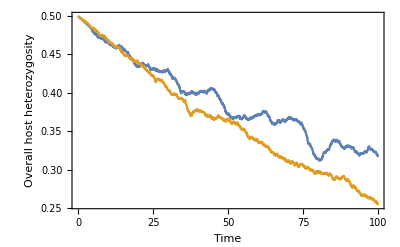

```mathematica
Plot[{meanHInt[pars2,τ,5],meanHInt[pars2N,τ,5]},{τ,0,τMax/.pars2},Frame-> True,FrameLabel-> {"Time","Overall host heterozygosity"}]
```

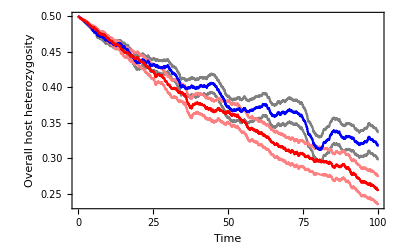

```mathematica
Show[
Plot[{meanHInt[pars2,τ,5]-SEHInt[pars2,τ,5],meanHInt[pars2N,τ,5]-SEHInt[pars2N,τ,5]},{τ,0,τMax/.pars2},Frame-> True,FrameLabel-> {"Time","Overall host heterozygosity"},PlotStyle-> {Directive[Gray],Directive[Pink]}],Plot[{meanHInt[pars2,τ,5]+SEHInt[pars2,τ,5],meanHInt[pars2N,τ,5]+SEHInt[pars2N,τ,5]},{τ,0,τMax/.pars2},Frame-> True,FrameLabel-> {"Time","Overall host heterozygosity"},PlotStyle-> {Directive[Gray],Directive[Pink]}],
Plot[{meanHInt[pars2,τ,5],meanHInt[pars2N,τ,5]},{τ,90,τMax/.pars2},Frame-> True,FrameLabel-> {"Time","Overall host heterozygosity"},PlotStyle-> {Directive[Blue],Directive[Red]}]]
```

```mathematica
RegionPlot[{meanHInt[pars2,τ,5],meanHInt[pars2,τ,5]+SEHInt[pars2,τ,5]},{τ,0,τMax/.pars2},Frame-> True,FrameLabel-> {"Time","Overall host heterozygosity"},PlotPoints->50, Mesh-> All, MaxRecursion->0]
```

$Aborted

```mathematica
names={"t","meanHet","seHet","meanHetN","seHetN"};
vals=Transpose[
{Table[τ,{τ,0,τMax/.pars2}],
Table[meanHInt[pars2,τ,5],{τ,0,τMax/.pars2}],
Table[SEHInt[pars2,τ,5],{τ,0,τMax/.pars2}],
Table[meanHInt[pars2N,τ,5],{τ,0,τMax/.pars2N}],
Table[SEHInt[pars2N,τ,5],{τ,0,τMax/.pars2N}]}];
valList=Prepend[vals,names]//TableForm
```

t | meanHet | seHet | meanHetN | seHetN
0 | 0.499992 | 1.07204×10^-6 | 0.499992 | 1.07204×10^-6
1 | 0.496778 | 0.000417503 | 0.496494 | 0.000447376
2 | 0.492878 | 0.00098711 | 0.49377 | 0.00106045
3 | 0.490168 | 0.00162081 | 0.490981 | 0.00129596
4 | 0.485543 | 0.00190158 | 0.486654 | 0.00195165
5 | 0.479899 | 0.00230094 | 0.483989 | 0.00223514
6 | 0.476872 | 0.00262748 | 0.48182 | 0.00240297
7 | 0.472802 | 0.00316543 | 0.47648 | 0.00312733
8 | 0.470891 | 0.00389025 | 0.474605 | 0.00347684
9 | 0.467902 | 0.00455443 | 0.472504 | 0.00341582
10 | 0.46578 | 0.00458745 | 0.46832 | 0.00377519
11 | 0.46277 | 0.00425488 | 0.465662 | 0.00415899
12 | 0.459988 | 0.00417264 | 0.460995 | 0.00501499
13 | 0.459977 | 0.00432281 | 0.460757 | 0.0052278
14 | 0.460845 | 0.00447238 | 0.457336 | 0.00551457
15 | 0.45649 | 0.00490198 | 0.451217 | 0.00643314
16 | 0.452407 | 0.00618386 | 0.449068 | 0.00641766
17 | 0.44924 | 0.00669428 | 0.446705 | 0.00702704
18 | 0.444086 | 0.00766849 | 0.444074 | 0.00736318
19 | 0.437675 | 0.00849161 | 0.440681 | 0.00809822
20 | 0.434808 | 0.00916944 | 0.441129 | 0.00843669
21 | 0.438183 | 0.00845131 | 0.435696 | 0.00867268
22 | 0.43763 | 0.00810224 | 0.433389 | 0.00914208
23 | 0.43583 | 0.00755717 | 0.429329 | 0.00945831
24 | 0.432586 | 0.00811288 | 0.42616 | 0.00985335
25 | 0.431368 | 0.00845168 | 0.422556 | 0.0102912
26 | 0.429498 | 0.00848833 | 0.414569 | 0.0107217
27 | 0.428596 | 0.00915058 | 0.417216 | 0.0105511
28 | 0.427813 | 0.00969187 | 0.416494 | 0.0102734
29 | 0.428043 | 0.00942595 | 0.408583 | 0.0107189
30 | 0.429826 | 0.00857957 | 0.40356 | 0.0113574
31 | 0.423457 | 0.00914496 | 0.399019 | 0.0119973
32 | 0.418695 | 0.00974007 | 0.398654 | 0.0121648
33 | 0.413555 | 0.0101007 | 0.396182 | 0.012453
34 | 0.404413 | 0.0108685 | 0.393173 | 0.0123906
35 | 0.40162 | 0.0108741 | 0.391049 | 0.0123073
36 | 0.399168 | 0.0115136 | 0.385345 | 0.0125701
37 | 0.399337 | 0.0119561 | 0.375284 | 0.0131123
38 | 0.401494 | 0.012004 | 0.3709 | 0.0134629
39 | 0.398524 | 0.0122852 | 0.37665 | 0.0133523
40 | 0.399216 | 0.0119128 | 0.377722 | 0.0136303
41 | 0.401774 | 0.0116079 | 0.37542 | 0.0140737
42 | 0.402493 | 0.011372 | 0.374933 | 0.0142033
43 | 0.399786 | 0.0121993 | 0.371078 | 0.0148124
44 | 0.404076 | 0.0127146 | 0.370348 | 0.0144685
45 | 0.404709 | 0.0130869 | 0.367391 | 0.0147283
46 | 0.400846 | 0.0133874 | 0.366196 | 0.0145971
47 | 0.394332 | 0.0136795 | 0.369717 | 0.0146785
48 | 0.385815 | 0.0139719 | 0.366519 | 0.0149375
49 | 0.37814 | 0.0144287 | 0.363653 | 0.0154395
50 | 0.371882 | 0.014891 | 0.365274 | 0.015102
51 | 0.367834 | 0.0151074 | 0.360877 | 0.0153975
52 | 0.366556 | 0.0154175 | 0.362007 | 0.0153553
53 | 0.368934 | 0.0156311 | 0.358919 | 0.0159202
54 | 0.366463 | 0.0159247 | 0.355771 | 0.0161304
55 | 0.368537 | 0.0161831 | 0.351651 | 0.0159485
56 | 0.367229 | 0.0159726 | 0.348685 | 0.0160832
57 | 0.364978 | 0.0155465 | 0.341486 | 0.0164185
58 | 0.366504 | 0.0156452 | 0.342155 | 0.0161362
59 | 0.369698 | 0.0158461 | 0.338845 | 0.0161896
60 | 0.371251 | 0.0158012 | 0.337163 | 0.0163434
61 | 0.371727 | 0.0157647 | 0.335495 | 0.0166231
62 | 0.374706 | 0.0156575 | 0.332464 | 0.0169804
63 | 0.372866 | 0.0153122 | 0.328892 | 0.0171498
64 | 0.364957 | 0.0156855 | 0.325883 | 0.0171929
65 | 0.360015 | 0.0155211 | 0.32218 | 0.0174873
66 | 0.3597 | 0.015476 | 0.319064 | 0.0177708
67 | 0.364923 | 0.0157509 | 0.316242 | 0.0178426
68 | 0.364208 | 0.0161254 | 0.315423 | 0.0179816
69 | 0.362596 | 0.0169521 | 0.313708 | 0.0179385
70 | 0.366713 | 0.0171514 | 0.311329 | 0.01808
71 | 0.367774 | 0.016996 | 0.308404 | 0.0181446
72 | 0.364997 | 0.0169082 | 0.307256 | 0.0181666
73 | 0.363997 | 0.0168285 | 0.308492 | 0.0181993
74 | 0.360282 | 0.0173047 | 0.305902 | 0.0182359
75 | 0.355367 | 0.0177601 | 0.306402 | 0.0181687
76 | 0.34721 | 0.0178737 | 0.301879 | 0.0183046
77 | 0.333341 | 0.0177056 | 0.301813 | 0.0183973
78 | 0.32748 | 0.0171661 | 0.2995 | 0.0182479
79 | 0.318781 | 0.0170951 | 0.294877 | 0.0183618
80 | 0.313313 | 0.017342 | 0.295826 | 0.018282
81 | 0.31311 | 0.0178026 | 0.2957 | 0.0184533
82 | 0.321447 | 0.0182735 | 0.29419 | 0.0184008
83 | 0.324 | 0.0183472 | 0.294175 | 0.0186512
84 | 0.330906 | 0.0183581 | 0.294085 | 0.0186157
85 | 0.337694 | 0.0180743 | 0.287322 | 0.0186864
86 | 0.337656 | 0.0177617 | 0.289612 | 0.0188524
87 | 0.336886 | 0.0177299 | 0.288371 | 0.0191092
88 | 0.329403 | 0.0177435 | 0.289677 | 0.0190136
89 | 0.327554 | 0.0179226 | 0.288639 | 0.0188144
90 | 0.330365 | 0.0183991 | 0.286939 | 0.0189086
91 | 0.329542 | 0.0182258 | 0.27865 | 0.0191029
92 | 0.326619 | 0.0178765 | 0.277617 | 0.0192104
93 | 0.321296 | 0.0176459 | 0.272779 | 0.0190957
94 | 0.319613 | 0.0177276 | 0.269521 | 0.019406
95 | 0.320343 | 0.0185422 | 0.266019 | 0.0193636
96 | 0.323315 | 0.0190222 | 0.265607 | 0.019627
97 | 0.329983 | 0.0194371 | 0.2634 | 0.0197871
98 | 0.326519 | 0.0195793 | 0.262638 | 0.0199901
99 | 0.323019 | 0.019473 | 0.257926 | 0.0197783
100 | 0.31808 | 0.0192266 | 0.253844 | 0.0197877

```mathematica
Export["~/Desktop/Mideo.lab2/Coevolution/Data sets/Data_2_List.csv",valList,"CSV"];
```

```mathematica
valList
```

t | meanHet | seHet | meanHetN | seHetN
0 | 0.499992 | 1.07204×10^-6 | 0.499992 | 1.07204×10^-6
1 | 0.496778 | 0.000417503 | 0.496494 | 0.000447376
2 | 0.492878 | 0.00098711 | 0.49377 | 0.00106045
3 | 0.490168 | 0.00162081 | 0.490981 | 0.00129596
4 | 0.485543 | 0.00190158 | 0.486654 | 0.00195165
5 | 0.479899 | 0.00230094 | 0.483989 | 0.00223514
6 | 0.476872 | 0.00262748 | 0.48182 | 0.00240297
7 | 0.472802 | 0.00316543 | 0.47648 | 0.00312733
8 | 0.470891 | 0.00389025 | 0.474605 | 0.00347684
9 | 0.467902 | 0.00455443 | 0.472504 | 0.00341582
10 | 0.46578 | 0.00458745 | 0.46832 | 0.00377519
11 | 0.46277 | 0.00425488 | 0.465662 | 0.00415899
12 | 0.459988 | 0.00417264 | 0.460995 | 0.00501499
13 | 0.459977 | 0.00432281 | 0.460757 | 0.0052278
14 | 0.460845 | 0.00447238 | 0.457336 | 0.00551457
15 | 0.45649 | 0.00490198 | 0.451217 | 0.00643314
16 | 0.452407 | 0.00618386 | 0.449068 | 0.00641766
17 | 0.44924 | 0.00669428 | 0.446705 | 0.00702704
18 | 0.444086 | 0.00766849 | 0.444074 | 0.00736318
19 | 0.437675 | 0.00849161 | 0.440681 | 0.00809822
20 | 0.434808 | 0.00916944 | 0.441129 | 0.00843669
21 | 0.438183 | 0.00845131 | 0.435696 | 0.00867268
22 | 0.43763 | 0.00810224 | 0.433389 | 0.00914208
23 | 0.43583 | 0.00755717 | 0.429329 | 0.00945831
24 | 0.432586 | 0.00811288 | 0.42616 | 0.00985335
25 | 0.431368 | 0.00845168 | 0.422556 | 0.0102912
26 | 0.429498 | 0.00848833 | 0.414569 | 0.0107217
27 | 0.428596 | 0.00915058 | 0.417216 | 0.0105511
28 | 0.427813 | 0.00969187 | 0.416494 | 0.0102734
29 | 0.428043 | 0.00942595 | 0.408583 | 0.0107189
30 | 0.429826 | 0.00857957 | 0.40356 | 0.0113574
31 | 0.423457 | 0.00914496 | 0.399019 | 0.0119973
32 | 0.418695 | 0.00974007 | 0.398654 | 0.0121648
33 | 0.413555 | 0.0101007 | 0.396182 | 0.012453
34 | 0.404413 | 0.0108685 | 0.393173 | 0.0123906
35 | 0.40162 | 0.0108741 | 0.391049 | 0.0123073
36 | 0.399168 | 0.0115136 | 0.385345 | 0.0125701
37 | 0.399337 | 0.0119561 | 0.375284 | 0.0131123
38 | 0.401494 | 0.012004 | 0.3709 | 0.0134629
39 | 0.398524 | 0.0122852 | 0.37665 | 0.0133523
40 | 0.399216 | 0.0119128 | 0.377722 | 0.0136303
41 | 0.401774 | 0.0116079 | 0.37542 | 0.0140737
42 | 0.402493 | 0.011372 | 0.374933 | 0.0142033
43 | 0.399786 | 0.0121993 | 0.371078 | 0.0148124
44 | 0.404076 | 0.0127146 | 0.370348 | 0.0144685
45 | 0.404709 | 0.0130869 | 0.367391 | 0.0147283
46 | 0.400846 | 0.0133874 | 0.366196 | 0.0145971
47 | 0.394332 | 0.0136795 | 0.369717 | 0.0146785
48 | 0.385815 | 0.0139719 | 0.366519 | 0.0149375
49 | 0.37814 | 0.0144287 | 0.363653 | 0.0154395
50 | 0.371882 | 0.014891 | 0.365274 | 0.015102
51 | 0.367834 | 0.0151074 | 0.360877 | 0.0153975
52 | 0.366556 | 0.0154175 | 0.362007 | 0.0153553
53 | 0.368934 | 0.0156311 | 0.358919 | 0.0159202
54 | 0.366463 | 0.0159247 | 0.355771 | 0.0161304
55 | 0.368537 | 0.0161831 | 0.351651 | 0.0159485
56 | 0.367229 | 0.0159726 | 0.348685 | 0.0160832
57 | 0.364978 | 0.0155465 | 0.341486 | 0.0164185
58 | 0.366504 | 0.0156452 | 0.342155 | 0.0161362
59 | 0.369698 | 0.0158461 | 0.338845 | 0.0161896
60 | 0.371251 | 0.0158012 | 0.337163 | 0.0163434
61 | 0.371727 | 0.0157647 | 0.335495 | 0.0166231
62 | 0.374706 | 0.0156575 | 0.332464 | 0.0169804
63 | 0.372866 | 0.0153122 | 0.328892 | 0.0171498
64 | 0.364957 | 0.0156855 | 0.325883 | 0.0171929
65 | 0.360015 | 0.0155211 | 0.32218 | 0.0174873
66 | 0.3597 | 0.015476 | 0.319064 | 0.0177708
67 | 0.364923 | 0.0157509 | 0.316242 | 0.0178426
68 | 0.364208 | 0.0161254 | 0.315423 | 0.0179816
69 | 0.362596 | 0.0169521 | 0.313708 | 0.0179385
70 | 0.366713 | 0.0171514 | 0.311329 | 0.01808
71 | 0.367774 | 0.016996 | 0.308404 | 0.0181446
72 | 0.364997 | 0.0169082 | 0.307256 | 0.0181666
73 | 0.363997 | 0.0168285 | 0.308492 | 0.0181993
74 | 0.360282 | 0.0173047 | 0.305902 | 0.0182359
75 | 0.355367 | 0.0177601 | 0.306402 | 0.0181687
76 | 0.34721 | 0.0178737 | 0.301879 | 0.0183046
77 | 0.333341 | 0.0177056 | 0.301813 | 0.0183973
78 | 0.32748 | 0.0171661 | 0.2995 | 0.0182479
79 | 0.318781 | 0.0170951 | 0.294877 | 0.0183618
80 | 0.313313 | 0.017342 | 0.295826 | 0.018282
81 | 0.31311 | 0.0178026 | 0.2957 | 0.0184533
82 | 0.321447 | 0.0182735 | 0.29419 | 0.0184008
83 | 0.324 | 0.0183472 | 0.294175 | 0.0186512
84 | 0.330906 | 0.0183581 | 0.294085 | 0.0186157
85 | 0.337694 | 0.0180743 | 0.287322 | 0.0186864
86 | 0.337656 | 0.0177617 | 0.289612 | 0.0188524
87 | 0.336886 | 0.0177299 | 0.288371 | 0.0191092
88 | 0.329403 | 0.0177435 | 0.289677 | 0.0190136
89 | 0.327554 | 0.0179226 | 0.288639 | 0.0188144
90 | 0.330365 | 0.0183991 | 0.286939 | 0.0189086
91 | 0.329542 | 0.0182258 | 0.27865 | 0.0191029
92 | 0.326619 | 0.0178765 | 0.277617 | 0.0192104
93 | 0.321296 | 0.0176459 | 0.272779 | 0.0190957
94 | 0.319613 | 0.0177276 | 0.269521 | 0.019406
95 | 0.320343 | 0.0185422 | 0.266019 | 0.0193636
96 | 0.323315 | 0.0190222 | 0.265607 | 0.019627
97 | 0.329983 | 0.0194371 | 0.2634 | 0.0197871
98 | 0.326519 | 0.0195793 | 0.262638 | 0.0199901
99 | 0.323019 | 0.019473 | 0.257926 | 0.0197783
100 | 0.31808 | 0.0192266 | 0.253844 | 0.0197877